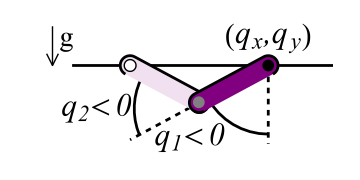
-Graphics-

Based on the model above [1] with continuation results from [2].  The code presented here is mainly to test the NLink code against a known system.  A simpler tutorial version of how to use NLink can be found in GoswamiEtAl.nb.

[1] Rosa,N., A.Barber, R.D.Gregg, and K.M.Lynch, "Stable open-loop brachiation on a vertical wall", Robotics and Automation (ICRA),2012.
 
[2] Rosa, N., and K. M. Lynch, “The Passive Dynamics of Walking and Brachiating Robots: Results on the Topology and Stability of Passive Gaits”, International Conference on Climbing and Walking Robots, 2013.

## Recursive Newton-Euler + Composite Rigid Body Algorithm

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../"];
SetOptions[NDSolve, AccuracyGoal-> 13, PrecisionGoal-> 13, 
Compiled-> False, MaxSteps-> Infinity];
<<"NLink`";
SetDirectory[NotebookDirectory[]];
```

```mathematica
n = 2; (* # of bodies *)

(* physical parameters in SI units used in [1] *)
(* we'll place them in a function for now, so we can run tests symbolically *)
PhysicalParameters[] := Module[{},
(* mass and inertia *)
m1=3.083276839957533; (* link mass *)
m2=3.083276839957533;
I1=5.386568898408416*^-2; (* inertia about c.o.m *)I2=5.386568898408416*^-2;

(* lengths *)
L1=0.610; (* link length *)
L2=0.610;
r2=6.37687066165708*^-2; (* distance to c.o.m *)
r1=L1-r2;

(* gravity *)
g=9.81;

(* scaling factors *)
d = L1 + L2; (* length *)
dt = Sqrt[d/g];
du = g m2 r2;
]
```

```mathematica
frames = ConstantArray[0, {n, 6}];
(* frames is a list of spatial vectors {rx, ry, rz, px, py, pz} defining the location of frame i in frame (i-1) coordinates when the robot is at its "home" configuration. *)
frames⟦2, 5⟧ = -L1/d;

frames // N // MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -(1. L1)/d | 0.)

```mathematica
inertia = ConstantArray[0, {n, 10}];
(* inertia is a list of mass parameters about the center of mass and their location {m, rx, ry, rz, px, py, pz, Ixx, Iyy, Izz} of link i in link i coordinates; cross inertia terms, e.g., Ixy, are also supported. *)

inertia⟦1, {1, 6, 10}⟧ = {d m1/(m2 r2) , -r1/d, I1/ (d m2 r2)};
inertia⟦2, {1, 6, 10}⟧ =  {d m2/(m2 r2), -r2/d, I2/ (d m2 r2)};

inertia // N// MatrixForm
```

((d m1)/(m2 r2) | 0. | 0. | 0. | 0. | -(1. r1)/d | 0. | 0. | 0. | I1/(d m2 r2)
d/r2 | 0. | 0. | 0. | 0. | -(1. r2)/d | 0. | 0. | 0. | I2/(d m2 r2))

```mathematica
(* robot description *)
parent = Range[2]-1; (* kinematic chain *)
joints = {"pln", "rz"};
nd = 2Length@NLink`Private`ExpandJoints[joints] + 4;
b = {{1,0}, {1,0}};
r = {{{0,0,0,1,0,0}, {0,0,0,1,0,0}}, {{0,0,0,0,1,0}, {0,0,0,0,1,0}}};
SetModel[joints, parent, {b,r}, {0, g dt^2/d, 0}, inertia, frames, nd];
```

```mathematica
Quiet@NLink`Private`F[x, u];
c[x_] := Evaluate[NLink`Private`c  // Simplify];
M[x_] := Evaluate[
NLink`Private`XL = NLink`Private`Xip[x];
NLink`Private`M = NLink`Private`ZM;
NLink`Private`IC = NLink`Private`𝕀;
NLink`Private`JSIM[x];
NLink`Private`M+LowerTriangularize[NLink`Private`M, -1]ᵀ // Simplify
];
```

## Euler-Lagrange Derivation [1]

#### Warning: the following code manipulates the $ContextPath and assumes that the Global context appears once at the end of the list.

```mathematica
(*we'll create a new context to avoid naming collisions.*)
Begin["EL`"];
$ContextPath = $ContextPath⟦;;-2⟧;

d = Global`d;
dt = Global`dt;
mr = Global`m2 Global`r2; 

g = dt^2/d Global`g ;
m1 = d/mr Global`m1;
m2 = d/mr Global`m2;
I1 = Global`I1/(d mr);
I2 = Global`I2/(d mr);
r1 = Global`r1/d;
r2 = Global`r2/d;
L1 = Global`L1/d;
L2 = Global`L2/d;

Off[Part::partd];
Off[Part::take];
(* x = {qx, qy, q1, q2, dqx, dqy, dq1, dq2} *)
nq = 4; (* # of configuration variables *)
X = Array[x⟦#⟧&, 2nq];
U = Array[u⟦#⟧&, nq];

p0[x_] := {x⟦1⟧, x⟦2⟧};
p1[x_] := p0[x] + {r1 Sin[x⟦3⟧], -r1 Cos[x⟦3⟧]};
p2[x_] := p0[x] + {L1 Sin[x⟦3⟧], -L1 Cos[x⟦3⟧]};
p3[x_] := p2[x] + {r2 Sin[x⟦3⟧+x⟦4⟧], -r2 Cos[x⟦3⟧+x⟦4⟧]};
p4[x_] := p2[x] + {L2 Sin[x⟦3⟧+x⟦4⟧], -L2 Cos[x⟦3⟧+x⟦4⟧]};

dp1[x_] := Evaluate[D[p1[X], {X⟦;;nq⟧}].X⟦nq+1;;⟧];
dp3[x_] := Evaluate[D[p3[X], {X⟦;;nq⟧}].X⟦nq+1;;⟧];

KE[x_] := Evaluate[1/2 (m1 dp1[X].dp1[X] + m2 dp3[X].dp3[X] + I1 X⟦7⟧^2 + I2 (X⟦7⟧+X⟦8⟧)^2)];

PE[x_] := Evaluate[g (m1 p1[X]⟦2⟧ + m2 p3[X]⟦2⟧)];

Γ[M_, var_, ind_] := Module[{i, j, k}, {i, j, k} = ind; 1/2(D[M⟦i,j⟧,var⟦k⟧] + D[M⟦i,k⟧,var⟦j⟧] - D[M⟦k,j⟧,var⟦i⟧])];

M[x_] := Evaluate[D[KE[X], {X⟦nq+1;;⟧, 2}]];

(* Coriolis and centrifugal forces *)
vp[x_] :=  Evaluate[Block[{M = M[X]}, Array[Sum[Γ[M, X, {#1,#2,k}]X⟦k+nq⟧, {k, nq}]&, {nq,nq}].X⟦nq+1;;⟧]];

(* potential forces *)
pf[x_] := Evaluate[D[PE[X], {X⟦1;;nq⟧}]];

c[x_] := Evaluate[vp[X]+pf[X]];

F[x_, u_]:= Evaluate[Inverse[M[X]].(U- c[X])];

dF[x_, u_]:= Evaluate[D[F[X, U], {Join[X,U]}]];

A[x_] := {{1,0,0,0}, {0,1,0,0}};
P[x_] := Evaluate[Block[{Minv = Inverse[M[X]]}, IdentityMatrix[nq] - Minv.A[X]ᵀ.Inverse[A[X].Minv.A[X]ᵀ].A[X]]];

dP[x_] := Evaluate[D[P[X], {Join[X,U]}]];

On[Part::partd];
On[Part::take];

$ContextPath = Append[$ContextPath,"Global`"];
End[];
```

## Test the two sets of equations

```mathematica
Quiet[M[x] - EL`M[x]] // Simplify // MatrixForm
Quiet[c[x] - EL`c[x]] // Simplify // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0
0
0
0)

```mathematica
(* now we switch to actual numerics, because symbolic computation takes forever *)
PhysicalParameters[];
x0 = RandomReal[{-10, 10}, NLink`Private`nx];
u0 = RandomReal[{-10, 10}, NLink`Private`nq];
F = NLink`Private`F[x0, u0];
dF = NLink`Private`dF[x0, u0, IdentityMatrix[{NLink`Private`nx, NLink`Private`nλ}], PadLeft[IdentityMatrix[NLink`Private`nq], {NLink`Private`nq, NLink`Private`nλ}]];

(* compare q^(..) *)
Norm[F- EL`F[x0, u0]]
(* compare df/dx and df/du *)
Norm[dF- EL`dF[x0, u0]]
(* compare constraints *)
Norm[NLink`Private`P[F] - EL`P[x0].EL`F[x0, u0]]
(* compare dP/dx and dP/du *)
Norm[NLink`Private`dP[F, dF] - (NLink`Private`dXb[EL`dP[x0], EL`F[x0, u0]]+EL`P[x0].EL`dF[x0, u0])]
```

2.17413×10^-13

1.60859×10^-12

3.06405×10^-13

8.5902×10^-13